# Biot-Savart Test file

### Author

Jan G. Korvink © 2021

## Warning: very slow n^2-complexity algorithm

### Next priority is to use a multipole expansion instead <<< NOT YET IMPLEMENTED.

### First we import the package that defines the functions.

```mathematica
fileName=StringJoin[NotebookDirectory[],"BiotSavart.m"];
Get[fileName]
```

### Next we check the names in the package. All names begin with “bs”, to signify Biot-Savart. We can click on an element to get the help text.

```mathematica
?bs*
```

```mathematica
??bsAbsMagneticInduction
```

### We now define some nice plot options for later general use

```mathematica
myOptions=List[AxesLabel->None,Axes->False,Frame->False,PlotRange->All,ContourShading->True,Contours->9,ColorFunction->"Pastel"];
myOptions=List[AxesLabel->None,Axes->False,Frame->False,PlotRange->All,ContourShading->True,Contours->9,ColorFunction->"BlueGreenYellow"];
```

### Here we demonstrate several current conducting segments and plot their fields.

#### SimpleLoop

```mathematica
segments=6;
δ=2π/segments;
SimpleLoopCoil=Table[{Sin[θ],Cos[θ],0},{θ,0,2π,2π/segments}];
Show[SimpleLoopCoilPlot=Graphics3D[{Orange,Tube[SimpleLoopCoil]}],Boxed->True,Axes->True]
```

-Graphics3D-

```mathematica
SimpleLoopCoilBField=bsUnitMagneticInduction[SimpleLoopCoil,{x,y,z}];
SimpleLoopCoilAbsBField=bsAbsMagneticInduction[SimpleLoopCoil,{x,y,z}];
```

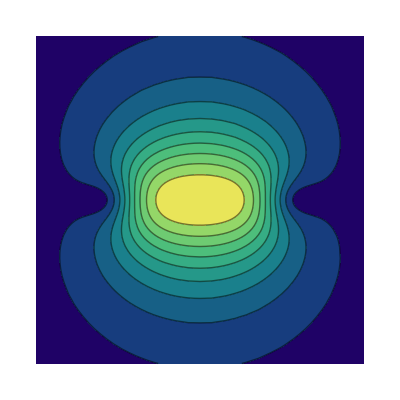

```mathematica
LoopField=ContourPlot[SimpleLoopCoilAbsBField/.y->0,{x,-2,2},{z,-2,2},Evaluate[myOptions]]
```

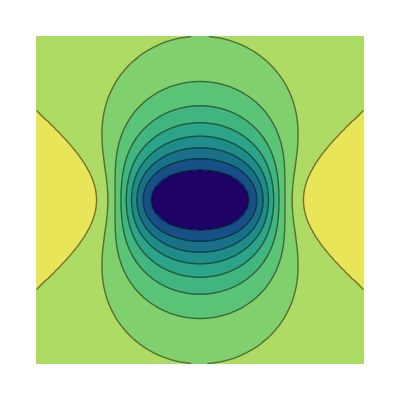

```mathematica
LoopField=ContourPlot[SimpleLoopCoilBField[[3]]/.y->0,{x,-2,2},{z,-2,2},Evaluate[myOptions]]
```

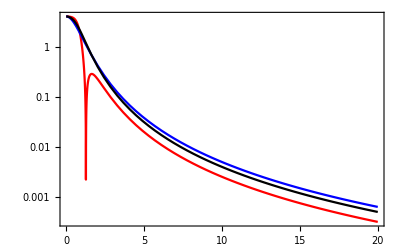

```mathematica
LogPlot[{SimpleLoopCoilAbsBField/.{x->α,y->0,z->0},SimpleLoopCoilAbsBField/.{x->0,y->0,z->α},SimpleLoopCoilAbsBField/.{x->α /Sqrt[2],y->0,z->α /Sqrt[2]}},{α,0,20},PlotRange->All,Frame->True,PlotStyle->{Red,Blue,Black}]
```

#### Alderman coil

```mathematica
Reverse[{{-f,-.1 f,-f},{f,-.1 f,-f}}]
```

{{f,-0.1 f,-f},{-f,-0.1 f,-f}}

0.0001

-Graphics3D-

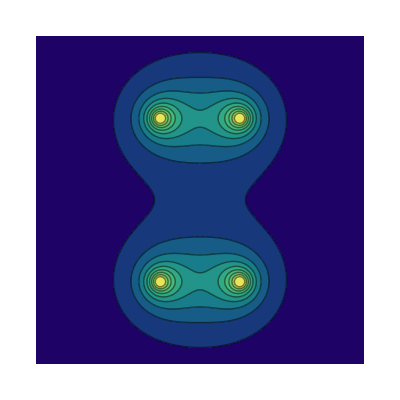

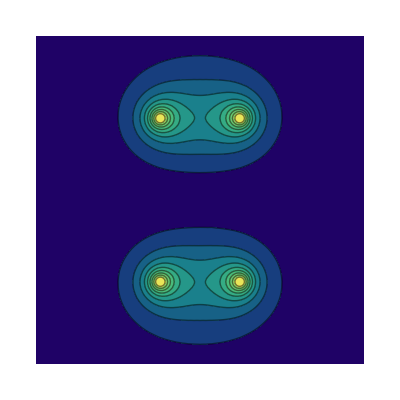

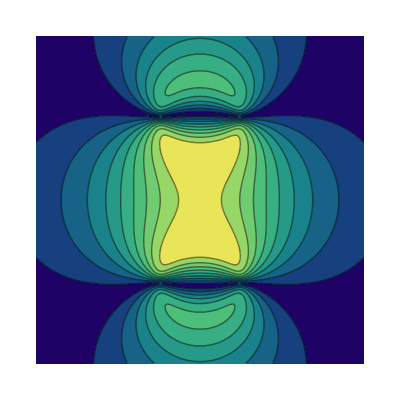

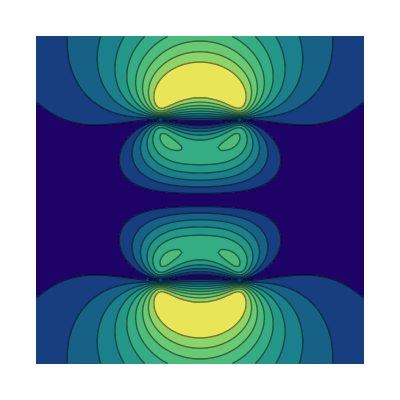

```mathematica
f=10^(-3);
g=f/2;
h=.1 f
l1={{-g,-h,-f},{g,-h,-f}};
l2={{-g,h,-f},{g,h,-f}};
l3={{-g,-h,f},{g,-h,f}};
l4={{-g,h,f},{g,h,f}};
shim01 = {l1,Reverse[l2],l3,Reverse[l4]};
shim02 = {l1,Reverse[l2],Reverse[l3],l4};
shim03 = {l1,l2,Reverse[l3],Reverse[l4]};
shim04 = {l1,l2,l3,l4};

Show[shim01Pic=Graphics3D[{Orange,Tube[shim01]}],Boxed->False, PlotRange->3{{-f/3,f/3},{-f/2,f/2},{-f/3,f/3}}]
shim01AbsBField=bsAbsMagneticInduction[{shim01},{x,y,z}];
shim02AbsBField=bsAbsMagneticInduction[{shim02},{x,y,z}];
shim03AbsBField=bsAbsMagneticInduction[{shim03},{x,y,z}];
shim04AbsBField=bsAbsMagneticInduction[{shim04},{x,y,z}];
ContourPlot[shim01AbsBField/.y->0,{x,-2f,2f},{z,-2f,2f},Evaluate[myOptions]]
ContourPlot[shim02AbsBField/.y->0,{x,-2f,2f},{z,-2f,2f},Evaluate[myOptions]]
ContourPlot[shim03AbsBField/.y->0,{x,-2f,2f},{z,-2f,2f},Evaluate[myOptions]]
ContourPlot[shim04AbsBField/.y->0,{x,-2f,2f},{z,-2f,2f},Evaluate[myOptions]]
```

```mathematica
SliceContourPlot3D[shim01AbsBField/.y->0,"CenterPlanes",{x,-2f,2f},{y,-.1f,.1f},{z,-2f,2f},ColorFunction->"BlueGreenYellow"]
SliceContourPlot3D[shim02AbsBField/.y->0,"CenterPlanes",{x,-2f,2f},{y,-.1f,.1f},{z,-2f,2f},ColorFunction->"BlueGreenYellow"]
SliceContourPlot3D[shim03AbsBField/.y->0,"CenterPlanes",{x,-2f,2f},{y,-.1f,.1f},{z,-2f,2f},ColorFunction->"BlueGreenYellow"]
SliceContourPlot3D[shim04AbsBField/.y->0,"CenterPlanes",{x,-2f,2f},{y,-.1f,.1f},{z,-2f,2f},ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»

```mathematica
ContourPlot3D[shim01AbsBField==500,{x,-2f,2f},{y,-.2f,.2f},{z,-2f,2f},ColorFunction->"BlueGreenYellow"]
```

-Graphics3D-

#### Solenoidal coil

```mathematica
numberOfWindings=3;
numberOfSegments=80;
endAngle=numberOfWindings 2 π;
generalPoint=(+1){Sin[θ],Cos[θ],θ/50};
connector={(generalPoint/.θ->endAngle)+{0,0,.1},(generalPoint/.θ->0)+{0,0,.1}};
SolinoidalCoil=Table[generalPoint,{θ,0,endAngle,2π/numberOfSegments}];
Show[Graphics3D[{Orange,Tube[SolinoidalCoil]}]]
```

-Graphics3D-

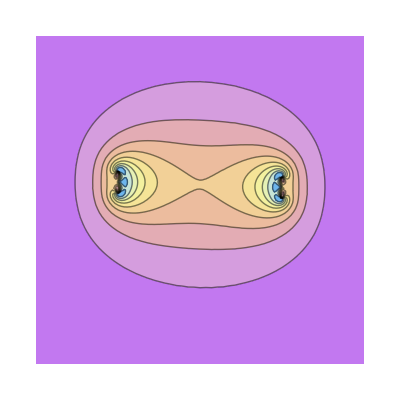

```mathematica
SolinoidalCoilAbsBField=bsAbsMagneticInduction[SolinoidalCoil,{x,y,z}];
ContourPlot[SolinoidalCoilAbsBField/.y->0,{x,-2,2},{z,-2,2},Evaluate[myOptions]]
```

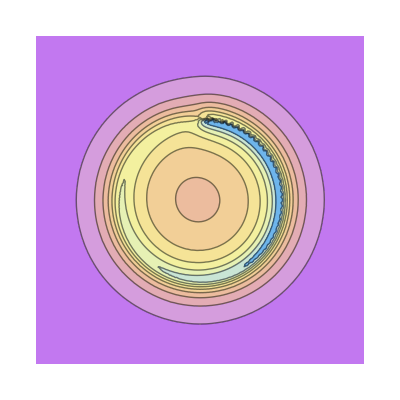

```mathematica
ContourPlot[SolinoidalCoilAbsBField/.z->0,{x,-2,2},{y,-2,2},Evaluate[myOptions]]
```

#### Helmholtz coil

```mathematica
numberOfWindings=1;
numberOfSegments=80;
endAngle=numberOfWindings 2 π;
generalPoint=(+1){Sin[θ],Cos[θ],θ/100};
connector={(generalPoint/.θ->endAngle)+{0,0,.1},(generalPoint/.θ->0)+{0,0,.1}};
bottomCoil=Join[{generalPoint-{1,0,.5}}/.θ->0,Table[generalPoint-{0,0,.5},{θ,0,endAngle,2π/numberOfSegments}],{generalPoint+{1,0,-.5}}/.θ->2π];
topCoil=Join[{generalPoint-{1,0,-0.5}}/.θ->0,Table[generalPoint+{0,0,.5},{θ,0,endAngle,2π/numberOfSegments}],{generalPoint+{1,0,0.5}}/.θ->2π];
HelmHoltzCoil={bottomCoil,topCoil};
Show[Graphics3D[{Orange,Tube[HelmHoltzCoil]}]]
```

-Graphics3D-

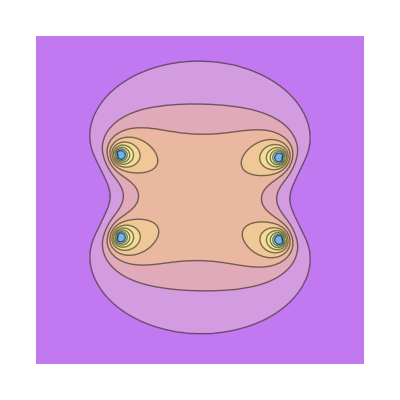

```mathematica
HelmHoltzCoilAbsBField=bsAbsMagneticInduction[HelmHoltzCoil,{x,y,z}];
ContourPlot[HelmHoltzCoilAbsBField/.y->0,{x,-2,2},{z,-2,2},Evaluate[myOptions]]
```

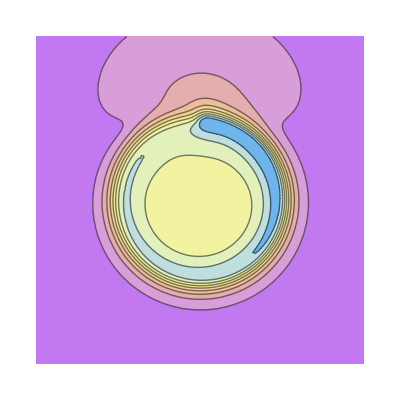

```mathematica
ContourPlot[HelmHoltzCoilAbsBField/.z->.4,{x,-2,2},{y,-2,2},Evaluate[myOptions]]
```

### For comparison, a dipole field.

#### Dipole field

```mathematica
DipoleVectorPotential=bsDipoleVectorPotential[{0,0,0},{x,y,z},{0,0,1}]
```

{-y/((x^2+y^2+z^2)^(3/2)),x/((x^2+y^2+z^2)^(3/2)),0}

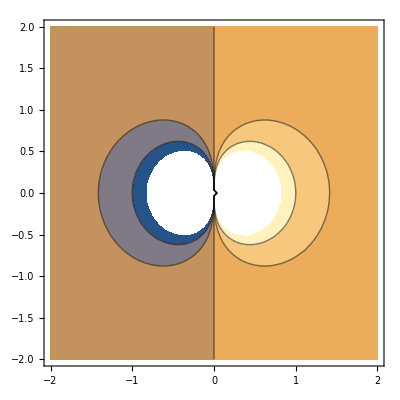

```mathematica
ContourPlot[ DipoleVectorPotential[[2]]/.y->0,{x,-2,2},{z,-2,2}]
```

```mathematica
DipoleBField=bsDipoleMagneticInduction[{{0,0,0},{1,0,0},{1,1,0},{0,1,0}},{x,y,z},{0,0,1}]
```

{(3 (-1+x) z)/(((-1+x)^2+(-1+y)^2+z^2)^(5/2))+(3 x z)/((x^2+(-1+y)^2+z^2)^(5/2))+(3 (-1+x) z)/(((-1+x)^2+y^2+z^2)^(5/2))+(3 x z)/((x^2+y^2+z^2)^(5/2)),(3 (-1+y) z)/(((-1+x)^2+(-1+y)^2+z^2)^(5/2))+(3 (-1+y) z)/((x^2+(-1+y)^2+z^2)^(5/2))+(3 y z)/(((-1+x)^2+y^2+z^2)^(5/2))+(3 y z)/((x^2+y^2+z^2)^(5/2)),(3 z^2)/(((-1+x)^2+(-1+y)^2+z^2)^(5/2))-1/(((-1+x)^2+(-1+y)^2+z^2)^(3/2))+(3 z^2)/((x^2+(-1+y)^2+z^2)^(5/2))-1/((x^2+(-1+y)^2+z^2)^(3/2))+(3 z^2)/(((-1+x)^2+y^2+z^2)^(5/2))-1/(((-1+x)^2+y^2+z^2)^(3/2))+(3 z^2)/((x^2+y^2+z^2)^(5/2))-1/((x^2+y^2+z^2)^(3/2))}

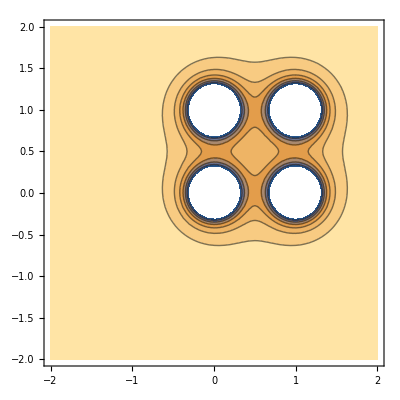

```mathematica
ContourPlot[ DipoleBField[[3]]/.z->0,{x,-2,2},{y,-2,2}]
```

### END OF THE FILE.